```mathematica
Clear[ndf,pdf,cdf]
ndf[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
(*pdf=Function[{θ,α},Evaluate[Integrate[2*π*ndf[θ,α]*Cos[θ]*Sin[θ],θ]]]*)
```

Function[{θ,α},(2 α^2)/((-1+α^2) (1+α^2+(-1+α^2) Cos[2 θ]))]

```mathematica
Clear[pdf]
(* Use a simpler version for the pdf, one without θ *)
(*pdf[μ_,α_]:=α^2/((α^2-1)(1+μ^2(α^2-1)))
cdf[μ_,α_]:=(1-μ^2)/(1+μ^2(α^2-1))*)

pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
```

Compute the difference of the PDFs of 2 neighbor pixels

```mathematica
(*Clear[α]
Integrate[2*π*(ndf[θ,α] - ndf[θ-β,α])*Cos[θ]*Sin[θ],θ]*)
```

```mathematica
ndf2[μ_,α_]:=α^2/(π*(μ^2*(α^2-1)+1)^2)
test[μ0_,α_]:=cdf[μ0,α]+ NIntegrate[2*π*(ndf2[μ,α] - ndf2[μ-μ0,α])*μ*√(1-μ^2),{μ,μ0,0}]
```

```mathematica
Manipulate[Plot[{test[μ0,α],cdf[μ0,α]},{α,0,1},PlotRange->{0,1}],{μ0,1,0}]
```

```mathematica
test[θ0_,α_]:=cdf[Cos[θ0],α]+ NIntegrate[2*π*(ndf[θ,α] - ndf[θ-θ0,α])*Cos[θ]*Sin[θ],{θ,θ0,π/2}]
Manipulate[Plot[{test[θ,α],cdf[Cos[θ],α]},{α,0,1},PlotRange->{-1,1}],{θ,0,π/2}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

```mathematica
pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
```

```mathematica
Manipulate[Show[Plot[pdf[θ,α]-pdf[θ0-θ,α],{θ,0,π/2},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
Manipulate[Show[Plot[pdf[θ,α]*pdf[θ0-θ,α],{θ,0,π/2},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ],{θ,0,π/2},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
```

```mathematica
Clear[α]
Integrate[(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],θ]
```

(α^2 (1/((-1+α^2) (1+α^2+(-1+α^2) Cos[2 θ]))-(ArcTan[(Sec[θ] ((1+α^2) Sin[θ]-(-1+α^2) Sin[θ-2 θ0]))/(2 α)] Sin[θ0])/(2 α^3)-(Sec[2 θ0] ((-1+α^2) Cos[θ0]^3+2 (-1+α^2) Sin[2 θ] Sin[θ0]+Cos[θ0] (1+3 α^2-3 (-1+α^2) Sin[θ0]^2)))/(4 α^2 (-1+α^2) (1+α^2+(-1+α^2) Cos[2 (θ-θ0)]))))/π

```mathematica
Manipulate[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
Manipulate[Plot[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]
```

Show the correlation

```mathematica
Manipulate[Show[Plot[ndf[θ,α]*Cos[θ]*ndf[θ-θ0,α]*Cos[θ-θ0],{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,0.05},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2

```mathematica
mipMax=8;
mu[mip_]:=1-1/3 2^(2(mip-mipMax))
2 * N[ArcCos[mu[8]]*180/π]
correl[θ_,θ0_,α_]:=ndf[θ,α]*Cos[θ]*ndf[θ-θ0,α]*Cos[θ-θ0]
correl[mu[8]/2,mu[8],1]
correl[π/4,π/2,1]
```

96.3794

Cos[1/3]^2/π^2

1/(2 π^2)

```mathematica
pipo[μ_,α_,v_]:=α^4*(μ^4)+α^2*(2*μ^2-2*μ^4-μ/(√v*π))+(1-2*μ^2+μ^4)
Manipulate[Plot[pipo[Cos[θ/2],α,1/(2 π^2)],{α,0,1}],{θ,0,π/2}]
```

```mathematica
pipo[Cos[π/4],1,1/(2 π^2)]
```

0

```mathematica
N[Solve[pipo[Cos[π/10],α,1/(2 π^2)]==0,α]]
```

{{α→-0.0884388},{α→0.0884388},{α→-1.19374},{α→1.19374}}

```mathematica
μ=Cos[π/10]
v=1/(2 π^2)
NSolve[α^4*(μ^4)+α^2*(2*μ^2-2*μ^4-μ/(√v*π))+(1-2*μ^2+μ^4)==0,α]
```

√(5/8+(√5)/8)

1/(2 π^2)

{{α→-1.19374},{α→-0.0884388},{α→0.0884388},{α→1.19374}}

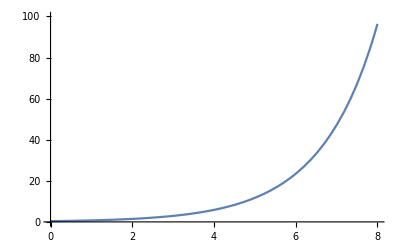

```mathematica
Plot[2*180/π ArcCos[mu[mip]],{mip,0,mipMax},PlotRange->{0,100}]
```

```mathematica
Table[N[Solve[pipo[mu[mip],α,1/(2 π^2)]==0,α]],{mip,0,mipMax}]
```

{{{α→-1.18921},{α→1.18921},{α→-8.5541×10^-6},{α→8.5541×10^-6}},{{α→-1.18921},{α→1.18921},{α→-0.0000342171},{α→0.0000342171}},{{α→-1.18922},{α→1.18922},{α→-0.00013688},{α→0.00013688}},{{α→-1.18924},{α→1.18924},{α→-0.000547711},{α→0.000547711}},{{α→-1.18934},{α→1.18934},{α→-0.00219387},{α→0.00219387}},{{α→-1.18973},{α→1.18973},{α→-0.00882434},{α→0.00882434}},{{α→-1.19126},{α→1.19126},{α→-0.0361012},{α→0.0361012}},{{α→-0.158921},{α→0.158921},{α→-1.19608},{α→1.19608}},{{α→-1.09236+0.238238 ⅈ},{α→1.09236-0.238238 ⅈ},{α→-1.09236-0.238238 ⅈ},{α→1.09236+0.238238 ⅈ}}}